Analisi della risposta libera per un sistema TC del II ordine

```mathematica
A=({{6, 1}, {-85, -8}})
```

{{6,1},{-85,-8}}

Determino gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{-1+6 ⅈ,-1-6 ⅈ}

Mi calcolo gli autovettori di A

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{-7-6 ⅈ,-7+6 ⅈ},{85,85}}

```mathematica
MatrixForm[T]
```

(-7-6 ⅈ | -7+6 ⅈ
85 | 85)

Mi calcolo la matrice di cambiamento di base che trasforma la matrice A nella sua forma canonica Scaling-Rotation

```mathematica
T̃=Transpose[{Re[T[[All,1]]],Im[T[[All,1]]]}]
```

{{-7,-6},{85,0}}

```mathematica
MatrixForm[T̃]
```

(-7 | -6
85 | 0)

```mathematica
Inverse[T̃].A.T̃
```

{{-1,6},{-6,-1}}

```mathematica
MatrixForm[Inverse[T̃].A.T̃]
```

(-1 | 6
-6 | -1)

Definisco lo stato iniziale e lo trasformo nella base delle colonne di T_tilde

```mathematica
Subscript[x, 0]={{2},{1}}
```

{{2},{1}}

```mathematica
MatrixForm[Subscript[x, 0]]
```

(2
1)

```mathematica
Subscript[z, 0]=Inverse[T̃].Subscript[x, 0]
```

{{1/85},{-59/170}}

Calcolo della risposta libera utilizzando la forma canonica Scaling-Rotation

```mathematica
σ=Re[λ[[1]]]
```

-1

```mathematica
ω=Im[λ[[1]]]
```

6

```mathematica
Subscript[x, l][t_]:=Simplify[T̃.({{Exp[σ t]Cos[ω t], Exp[σ t]Sin[ω t]}, {-Exp[σ t]Sin[ω t], Exp[σ t]Cos[ω t]}}).Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{{1/2 ⅇ^-t (4 Cos[6 t]+5 Sin[6 t])},{1/2 ⅇ^-t (2 Cos[6 t]-59 Sin[6 t])}}

```mathematica
MatrixForm[Subscript[x, l][t]]
```

(1/2 ⅇ^-t (4 Cos[6 t]+5 Sin[6 t])
1/2 ⅇ^-t (2 Cos[6 t]-59 Sin[6 t]))

Grafico delle componenti della risposta libera

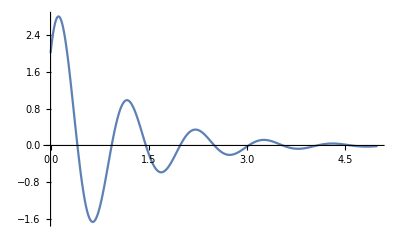

```mathematica
Plot[Subscript[x, l][t][[1]],{t,0,5},PlotRange->All]
```

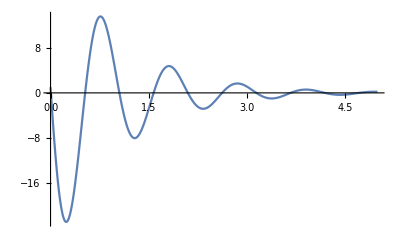

```mathematica
Plot[Subscript[x, l][t][[2]],{t,0,5},PlotRange->All]
```

Grafico della traiettoria del sistema (x1(t), x2(t))

```mathematica
Subscript[x, l][t][[1,1]]
```

1/2 ⅇ^-t (4 Cos[6 t]+5 Sin[6 t])

```mathematica
Subscript[x, l][t][[2,1]]
```

1/2 ⅇ^-t (2 Cos[6 t]-59 Sin[6 t])

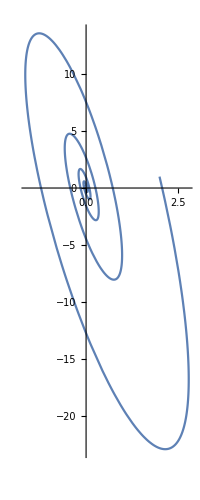

```mathematica
ParametricPlot[{Subscript[x, l][t][[1,1]],Subscript[x, l][t][[2,1]]},{t,0,5},PlotRange->All]
```